```mathematica
OutPutPath="ParralelD10";
SetDirectory[NotebookDirectory[]];
$P=2^31-1;
diffInvariants={mt2,s12,s123,s23,s234,s34,s345,s45,s56};
For[i=1,i<=9,i++,			
dhxbMatrices[diffInvariants[[i]]]=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/DEmatrix_d``",OutPutPath,diffInvariants[[i]]]]}]];
]
phasespacepoints=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/parameters",OutPutPath]]}]];
RationalReconstruct[a_]:=With[{v=LatticeReduce[{{a,1},{$P,0}}][[1]]},v[[1]]/v[[2]]];
```

```mathematica
powerReconstruct[pars_,FitVecIn_]:=Module[{pars2,AnsatzPowersNumi,FitVec,AnsatzPowersDeno,MatNumiPart,onevc,parsCutOne,reconstructedFit,AnsatzPowersDenoOne,
fit,solrule,MatDenoPart,Solset,FinalMat,sol3,Ansatz,MaxPower},
	MaxPower=9;
AnsatzPowersNumi=FrobeniusSolve[{1,1},MaxPower];
	AnsatzPowersDeno=FrobeniusSolve[{1,1},MaxPower];
	pars2=pars/.{x_Integer:>{x,1}};
	(*MatNumiPart=Parallelize@Outer[m31ExpDot,pars2,AnsatzPowersNumi,1];*)

	MatNumiPart=Table[Table[Times@@PowerMod[pars2[[i]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}],{i,1,Length[pars2]}];
	(*Table[Times@@PowerMod[pars2[[1]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}]//Echo;*)
	
	FitVec=Expand[-FitVecIn,Modulus->$P];
	onevc=Table[{1},MaxPower+1];
	parsCutOne=MapThread[Join,{pars2,Transpose[{FitVec}]}];
	AnsatzPowersDenoOne=MapThread[Join,{AnsatzPowersDeno,onevc}];

	(*MatDenoPart=Parallelize@Outer[m31ExpDot,parsCutOne,AnsatzPowersDenoOne,1];*)
	
	MatDenoPart=Table[Table[Times@@PowerMod[parsCutOne[[i]],AnsatzPowersDenoOne[[j]],$P],{j,1,Length[AnsatzPowersDenoOne]}],{i,1,Length[parsCutOne]}];
	
	FinalMat=Expand[MapThread[Join,{MatNumiPart,MatDenoPart}],Modulus->$P];

	
	sol3=NullSpace[FinalMat,Modulus->$P];
	Ansatz=Sum[fac[n]t^n,{n,0,MaxPower}]/Sum[fac[n+MaxPower+1]t^n,{n,0,MaxPower}];
	Solset=Cases[Ansatz,fac[___],Infinity];
	solrule=Thread[Rule[Solset,sol3[[1]]]];
	fit=Together[Ansatz/.solrule]//ExpandDenominator//ExpandNumerator;
	Return[Expand[fit,Modulus->$P]]
]
```

```mathematica
LaunchKernels[20];
```

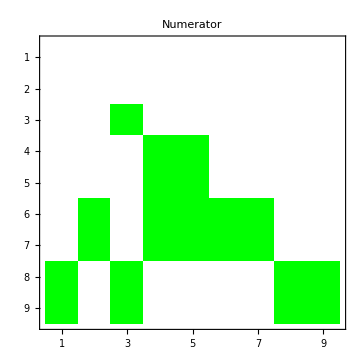
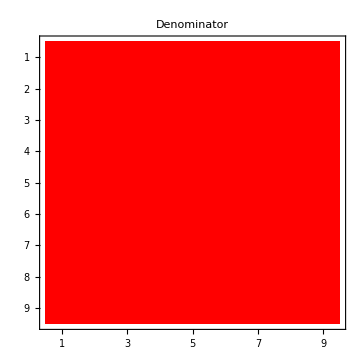
-Graphics- | -Graphics- |

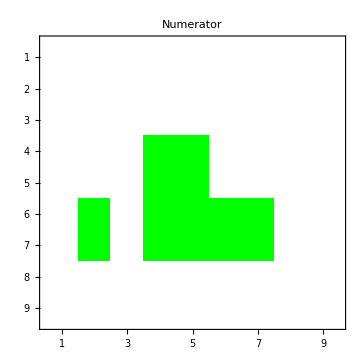
-Graphics- | -Graphics- |

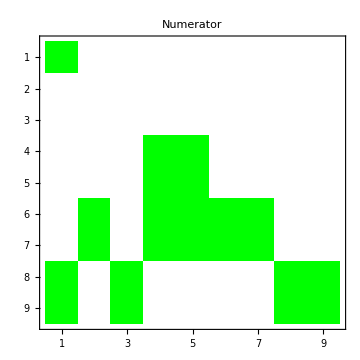
-Graphics- | -Graphics- |

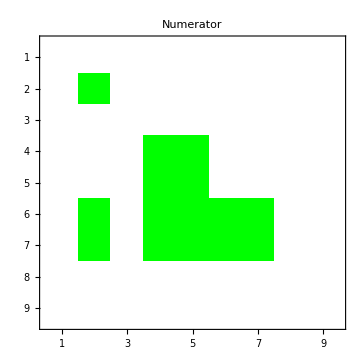
-Graphics- | -Graphics- |

-Graphics- | -Graphics- |

-Graphics- | -Graphics- |

-Graphics- | -Graphics- |

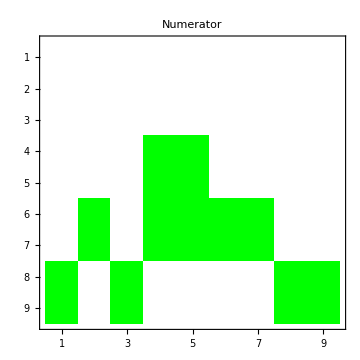
-Graphics- | -Graphics- |

-Graphics- | -Graphics- |

(1734594378 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 49635153 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1880880922 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1285247078 ϵ | 1941151320 ϵ | 0 | 0 | 0 | 0
0 | 0 | 0 | 1060381037 ϵ | 146061929 ϵ | 0 | 0 | 0 | 0
0 | 1971669898 ϵ | 0 | 1530875713 ϵ | 1161648698 ϵ | 1489039935 ϵ | 964234527 ϵ | 0 | 0
0 | 2005291132 ϵ | 0 | 1755468823 ϵ | 104171213 ϵ | 1925624437 ϵ | 1811769947 ϵ | 0 | 0
555396055 ϵ | 0 | 1351439851 ϵ | 0 | 0 | 0 | 0 | 1056531100 ϵ | 114333281 ϵ
1143388415 ϵ | 0 | 538619252 ϵ | 0 | 0 | 0 | 0 | 424090674 ϵ | 1484299735 ϵ)

```mathematica
BasisLength=9;
colors={-1->White,0->Red,1->Green,2->Blue,3->Yellow,4->Orange,5->RGBColor["#e09f7d"],6->RGBColor["#EF5D60"],7->RGBColor["#EC4067"],8->RGBColor["#A01A7D"],9->RGBColor["#703399"],10->RGBColor["#0B050F"]};
CutsA=1;
CutsB=BasisLength;
For[i=1,i<=9,i++,
MatReco[diffInvariants[[i]]]=ParallelTable[Quiet[Expand[powerReconstruct[phasespacepoints[[All,1]],dhxbMatrices[diffInvariants[[i]]][[All,pos]]]/.{t->4-2ϵ},Modulus->$P]],{pos,1,BasisLength^2}];
NumiPowers=Exponent[Numerator[MatReco[diffInvariants[[i]]]],ϵ]/.{-Infinity->-1};
DenoPowers=Exponent[Denominator[MatReco[diffInvariants[[i]]]],ϵ];
NumiPowersMat=NumiPowers//Normal;
DenoPowersMat=DenoPowers//Normal;
(*NonZerosPos=ReadList[FileNameJoin[{NotebookDirectory[],"files/NonZeroList.txt"}]];
NumiPowersMat=ConstantArray[-1,241^2];
NumiPowersMat[[NonZerosPos]]=NumiPowers;
DenoPowersMat=ConstantArray[-1,241^2];
DenoPowersMat[[NonZerosPos]]=DenoPowers;*)
P1=MatrixPlot[ArrayReshape[NumiPowersMat,{BasisLength,BasisLength}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Numerator",ImageSize->Medium];
P2=MatrixPlot[ArrayReshape[DenoPowersMat,{BasisLength,BasisLength}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Denominator",ImageSize->Medium];
L1=SwatchLegend[Values@colors[[2;;]],Keys@colors[[2;;]],LegendFunction->"Frame",LegendLayout->"Column",LegendLabel->diffInvariants[[i]]];
Print[Grid[{{P1,P2,L1}}]];
]
TestMat=Expand[Sum[RandomInteger[2^31-1]*ArrayReshape[MatReco[diffInvariants[[ii]]],{BasisLength,BasisLength}],{ii,1,9}], Modulus->2^31-1]//EchoFunction[MatrixForm];
```